```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

### Node Counting

```mathematica
NInfoNodes[b0_,b1_,b2_,b3_]:=
b0 8+b0 b1 7 10+b0 b1 b2 7 9 10+b0 b1 b2 b3 7 9 9 10
```

```mathematica
NInfoNodes[b0_,b1_,b2_,b3_]:=
b0(8+7b1(10+9b2(10+9b3(10))))
```

```mathematica
NGameStates[bn_,b0_,b1_,b2_,b3_,pfi_,pft_,pfl_,ftri_,ftt_,ftl_,rt_]:=
bn+b0 b0(pfi+pft+pfl(
bn+b1 b1(ftri+ftt+ftl(bn+b2 b2(ftri+ftt+ftl(bn+b3 b3(ftri+rt)))))))
```

```mathematica
NInfoNodes[b0_,b1_,b2_,b3_]:=NGameStates[0,√b0,√b1,√b2,√b3,8,0,7,10,0,9,0]
```

```mathematica
Do[If[
Round[NGameStates[bn,10,10,10,10,8,a,7,10,b,9,c]/10^10]==165
&&NGameStates[bn,1,1,1,1,8,a,7,10,b,9,c]==18496,Print[{bn,a,b,c}]],
{bn,0,1},
{a,0,30},
{b,0,30},
{c,0,50}]
```

{0,15,19,19}

{1,7,10,19}

```mathematica
NGameStates[0,1,1,1,1,8,0,7,10,0,9,0]
```

6378

```mathematica
NInfoNodes[1,1,1,1]
```

6378

```mathematica
NInfoNodes[10,10,10,10]
```

57337080

### Result Distributing

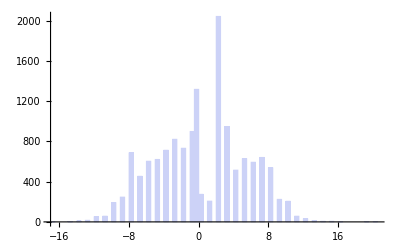

5.07181

```mathematica
{pots,winners}=Transpose[Import["pokerbreedinggrounds/bin/historiesfiltered2.txt","CSV"]];
pots[[Flatten[Position[winners,0]]]]*=2;(*ties had half the actual pot listed*)
Histogram[Inner[Times,pots/2,winners,List]]
StandardDeviation[Inner[Times,pots/2,winners,List]]//N
```

```mathematica
ties=N[pots[[Flatten[Position[winners,0]]]]];(*pots that were tied*)nonties=N[pots[[Flatten[Position[winners,1|-1]]]]];(*untied pots*)
Length[nonties]+Length[ties]==Length[pots]
```

True

(*preraked edge = 
     probability that I tie * 0 + probability that I don' t tie * 
       (probability that I win * total pot + probability that I lose * 0 - half the pot)   
  =
   prob[notie] * (prob[win] * avgpotsize - avgpotsize * 0.5)
  =
   prob[notie] * (prob[win] - 0.5) * avgpotsize
=== >
  prob[win] 
   = 0.5 + prerakededge / (prob[nonties] * avgpotsize)
   = 0.5 + prerakededge / (Length[nonties]/Length[pots] * Total[nonties]/Length[nonties])
   = 0.5 + prerakededge / (Total[nonties]/Length[pots])
   = 0.5 + prerakededge * (Length[pots]/Total[nonties])*)

```mathematica
multiplier=Length[pots]/Total[nonties];
GameResult[edge_,Rake_]:=Block[{r=RandomInteger[{1,Length[pots]}]},
If[r≤Length[ties],(Rake[ties[[r]]]-ties[[r]])/2,
r-=Length[ties];
If[RandomReal[]<0.5+multiplier edge/1000,Rake[nonties[[r]]],0]- nonties[[r]]/2]]
```

```mathematica
(*Mean[Table[GameResult[-100,Identity],{1000000}]]//Timing*)
```

```mathematica
Sort[Tally[winners],#1[[1]]<#2[[1]]&]//TableForm
```

-1 | 7417
0 | 274
1 | 6651

```mathematica
Sort[Tally[pots],#1[[1]]<#2[[1]]&]//TableForm
```

1 | 1317
2 | 1116
4 | 2791
6 | 1780
8 | 1258
10 | 1293
12 | 1239
14 | 1126
16 | 1254
18 | 484
20 | 413
22 | 123
24 | 85
26 | 31
28 | 18
30 | 8
32 | 1
34 | 2
38 | 1
40 | 2

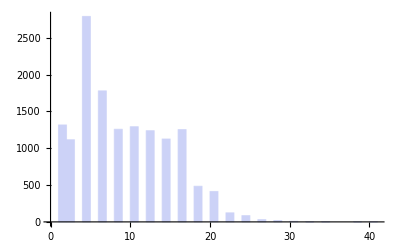

```mathematica
Histogram[pots]
```

### Analyze Tournies

```mathematica
Array[0&,10]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
ResetBotCounters[]:=(botcounters=Array[0&,125];)
BotCounter[stacki_]:=If[stacki≥48,Sum[botcounters[[i]],{i,49,Length[botcounters]}],botcounters[[stacki+1]]]
OneTourney[edge_]:=Catch[Block[
{bblind=(1/2)*{60,80,100,120,160,200,240,300,400,500,600,800,1000,1200,1600,2000,2400,3000},(*18 steps at each*)
balance=1500},
Do[Do[
Block[{maxgain=1500-Abs[balance-1500],result=GameResult[edge,Identity]*bblind[[i]]},
Block[{(*stacki=Floor[maxgain/(bblind[[i]]/2)],*)adjresult=Piecewise[{{maxgain, maxgain<result}, {result, -maxgain<=result<=maxgain}, {-maxgain, result<-maxgain}}]},
balance+=adjresult;
(*botcounters[[stacki+1]]++*)]];
If[balance>2999,Throw[1]];
If[balance<1,Throw[0]],
{18}],{i,1,Length[bblind]}]]]
```

```mathematica
TourneyWinRate[edge_,n_]:=Block[
{gameswon=0},
Do[gameswon+=OneTourney[edge],{n}];
N[gameswon/n]]
```

```mathematica
ResetBotCounters[]
```

```mathematica
BotCounter[48]/Total[botcounters]//N
```

0.564736

```mathematica
TourneyWinRate[20,10000]
```

0.5172

```mathematica
BotCounter[48]/Sum[botcounters[[i]],{i,1,47}]//N
```

1.33931

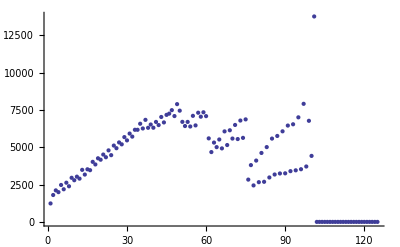

```mathematica
ListPlot[botcounters,PlotRange->All]
```

```mathematica
winrate=Table[{x,TourneyWinRate[x,100000]},{x,0,200,25}];
```

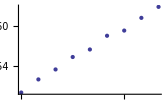

```mathematica
ListPlot[winrate]
```

```mathematica
FindFit[winrate,.5+a x,a,x]
```

{a→0.000651045}

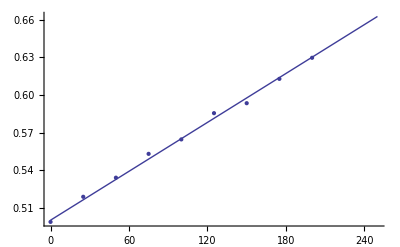

```mathematica
Show[ListPlot[winrate],Plot[Evaluate[.5+a x/.FindFit[winrate,.5+a x,a,x]],{x,0,250}]]
```

```mathematica
BreakEvenEdge[rakepct_]:=edge/.ToRules[Reduce[((0.5+a edge)/.FindFit[winrate,.5+a edge,a,edge])==(rakepct+1)/2,edge]]
```

```mathematica
BreakEvenEdge/@{.1/1,.15/2,.25/5,10/200,20/500,30/1000,50/2000}//Column
```

76.7996
57.5997
38.3998
38.3998
30.7198
23.0399
19.1999

```mathematica
TourneyWage[buyin_,rakeamt_,edgeplus_,perhour_:2]:=perhour (2buyin ((0.5+a x)/.FindFit[winrate,.5+a x,a,x]/.x->BreakEvenEdge[rakeamt/buyin]+edgeplus)-rakeamt-buyin)
```

```mathematica
With[{e=40},{TourneyWage[1,0.1,e,1],
TourneyWage[2,0.15,e,1],
TourneyWage[5,0.25,e,1],
TourneyWage[10,0.5,e,1],
TourneyWage[20,1,e,1],
TourneyWage[30,1.5,e,1],
TourneyWage[50,2.5,e,1],
TourneyWage[100,5,e,1],
TourneyWage[200,10,e,1],
TourneyWage[500,20,e,1],
TourneyWage[1000,30,e,1],
TourneyWage[2000,50,e,1]}]//Column
```

0.0520836
0.104167
0.260418
0.520836
1.04167
1.56251
2.60418
5.20836
10.4167
26.0418
52.0836
104.167

```mathematica
TourneyKelly[buyin_,rakeamt_,edgeplus_,i_:10000]:=  Variance[Table[2 buyin OneTourney[BreakEvenEdge[rakeamt/buyin]+edgeplus]-rakeamt-buyin,{i}]]/TourneyWage[buyin,rakeamt,edgeplus,1]
```

```mathematica
With[{e=20},{TourneyKelly[1,0.1,e],
TourneyKelly[2,0.15,e],
TourneyKelly[5,0.25,e],
TourneyKelly[10,0.5,e],
TourneyKelly[20,1,e],
TourneyKelly[30,1.5,e],
TourneyKelly[50,2.5,e],
TourneyKelly[100,5,e],
TourneyKelly[200,10,e],
TourneyKelly[500,20,e],
TourneyKelly[1000,30,e],
TourneyKelly[2000,50,e]}]//Column
```

37.8561
76.1286
190.456
380.814
762.602
1145.87
1903.43
3811.43
7633.76
19102.8
38220.8
76670.5

```mathematica
With[{e=40},{TourneyKelly[1,0.1,e],
TourneyKelly[2,0.15,e],
TourneyKelly[5,0.25,e],
TourneyKelly[10,0.5,e],
TourneyKelly[20,1,e],
TourneyKelly[30,1.5,e],
TourneyKelly[50,2.5,e],
TourneyKelly[100,5,e],
TourneyKelly[200,10,e],
TourneyKelly[500,20,e],
TourneyKelly[1000,30,e],
TourneyKelly[2000,50,e]}]//Column
```

18.6271
37.6638
95.168
190.293
379.356
570.679
948.809
1900.59
3795.4
9487.26
19057.8
38157.9

### Analyze Cash Game

```mathematica
Rake[potbb_,1]:=With[{x=potbb},Piecewise[{{x, x<5}, {x-0.25, 5≤x<10}, {x-0.5, 10≤x}}]]
Rake[potbb_,dolpbb_]:=With[{m=potbb dolpbb},Piecewise[{{m, m<10}, {m-0.5, 10≤m}}]]/dolpbb
```

```mathematica
CashGameRate[edge_,Rake_,n_:100000]:=Block[{balance=0},Do[balance+=GameResult[edge,Rake],{n}];balance/n]
```

```mathematica
{#,CashGameRate[#,Rake[#,30]&,1000000]}&/@Range[0,150,25]
```

{{0,-0.00990563},{25,0.0187731},{50,0.0404948},{75,0.0630538},{100,0.0900954},{125,0.111343},{150,0.143555}}

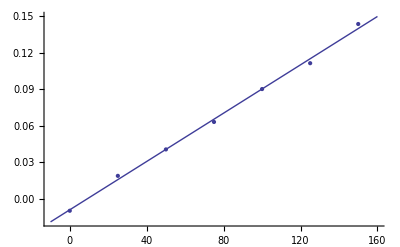

```mathematica
Show[ListPlot[%],Plot[Evaluate[Fit[%,{1,e},e]],{e,-10,160}]]
```

```mathematica
CashBreakEven[bblind_]:=e/.ToRules[Reduce[0==Fit[{#,CashGameRate[#,Rake[#,bblind]&,25000000]}&/@Range[0,150,25],{1,e},e]]]
```

```mathematica
(cashbreakeven={#,CashBreakEven[#]}&/@{1,2,3,5,8,10,15,30})//Grid
```

1 | 137.201
2 | 81.1587
3 | 70.2659
5 | 45.6097
8 | 29.9236
10 | 24.3284
15 | 16.1008
30 | 9.90008

```mathematica
CashGameWage[bblind_,breakevenedge_,edgeplus_,perhour_:50]:=perhour bblind CashGameRate[breakevenedge+edgeplus,Rake[#,bblind]&,25000000]
```

```mathematica
(cashwage20=MapThread[{#1,CashGameWage[#1,#2,20,50]}&,Transpose[cashbreakeven]])//Grid
```

1 | 1.02901
2 | 1.98436
3 | 3.05514
5 | 5.05751
8 | 8.43299
10 | 9.49015
15 | 15.5615
30 | 31.2683

```mathematica
(cashwage40=MapThread[{#1,CashGameWage[#1,#2,40,50]}&,Transpose[cashbreakeven]])//Grid
```

1 | 1.91811
2 | 3.84898
3 | 5.91624
5 | 9.53461
8 | 16.7185
10 | 19.0161
15 | 29.2028
30 | 64.3107

```mathematica
CashGameKelly[bblind_,breakevenedge_,wageperhour_,edgeplus_,perhour_:50,nhours_:5000]:=
1/wageperhour perhour  Variance[Table[bblind GameResult[breakevenedge+edgeplus,Rake[#,bblind]&],{perhour nhours}]]
```

```mathematica
MapThread[{#1,CashGameKelly[#1,#2,#4,20,50]}&,Transpose[Join[cashbreakeven,cashwage20,2]]]//Grid
```

1 | 1177.12
2 | 2499.55
3 | 3687.82
5 | 6243.12
8 | 9699.21
10 | 13419.7
15 | 18418.7
30 | 36825.3

```mathematica
MapThread[{#1,CashGameKelly[#1,#2,#4,40,50]}&,Transpose[Join[cashbreakeven,cashwage40,2]]]//Grid
```

1 | 626.452
2 | 1289.02
3 | 1906.48
5 | 3300.51
8 | 4874.66
10 | 6722.25
15 | 9825.44
30 | 18021.

#### Wages (+EV or not?)

```mathematica
With[{tw=Prepend[Table[TourneyWage[#1,#2,i],{i,1,Length[edges]}],{#1,#2}]&,
cw=Prepend[Table[CashGameWage[#1,i],{i,1,Length[edges]}],#1]&},
{Prepend[edges,Null],
tw[1,0.1],
tw[2,0.15],
tw[5,0.25],
tw[10,0.5],
tw[20,1],
tw[30,1.5],
tw[50,2.5],
tw[100,5],
tw[200,10],
cw[1],
cw[2],
cw[3],
cw[5],
cw[8],
cw[10],
cw[15],
cw[30]}]//Transpose//Grid
```

| {1,0.1} | {2,0.15} | {5,0.25} | {10,0.5} | {20,1} | {30,1.5} | {50,2.5} | {100,5} | {200,10} | 1 | 2 | 3 | 5 | 8 | 10 | 15 | 30
0 | -0.21276 | -0.32552 | -0.5638 | -1.1276 | -2.2552 | -3.3828 | -5.638 | -11.276 | -22.552 | -13.095 | -10.9255 | -28.678 | -32.325 | -19.65 | -35.7895 | -36.0807 | 4.046
25 | -0.15808 | -0.21616 | -0.2904 | -0.5808 | -1.1616 | -1.7424 | -2.904 | -5.808 | -11.616 | -10.0469 | -9.01525 | -3.30525 | -6.60175 | -5.3835 | 15.5395 | -12.068 | -57.2193
50 | -0.103 | -0.106 | -0.015 | -0.03 | -0.06 | -0.09 | -0.15 | -0.3 | -0.6 | -8.16263 | -6.55825 | -5.4975 | 6.47875 | 14.3095 | 43.9755 | 24.318 | 75.5942
75 | -0.0564 | -0.0128 | 0.218 | 0.436 | 0.872 | 1.308 | 2.18 | 4.36 | 8.72 | -6.8745 | -0.448 | 14.6223 | -3.03025 | 44.7683 | 48.1645 | 64.063 | 104.949
100 | 0.0016 | 0.1032 | 0.508 | 1.016 | 2.032 | 3.048 | 5.08 | 10.16 | 20.32 | -5.35875 | 5.766 | 5.59425 | 16.5805 | 51.0068 | 87.7945 | 142.627 | 204.953
125 | 0.04432 | 0.18864 | 0.7216 | 1.4432 | 2.8864 | 4.3296 | 7.216 | 14.432 | 28.864 | 0.77125 | 9.096 | 16.7957 | 35.7347 | 73.7943 | 92.5017 | 196.75 | 358.578
150 | 0.08888 | 0.27776 | 0.9444 | 1.8888 | 3.7776 | 5.6664 | 9.444 | 18.888 | 37.776 | 0.5725 | 10.231 | 19.1945 | 48.325 | 89.465 | 107.509 | 222.423 | 502.815
175 | 0.13884 | 0.37768 | 1.1942 | 2.3884 | 4.7768 | 7.1652 | 11.942 | 23.884 | 47.768 | 4.80413 | 18.4563 | 25.0117 | 68.4302 | 100.737 | 130.581 | 216.942 | 441.842
200 | 0.18428 | 0.46856 | 1.4214 | 2.8428 | 5.6856 | 8.5284 | 14.214 | 28.428 | 56.856 | 9.40788 | 24.891 | 37.4803 | 66.768 | 112.871 | 179.077 | 301.363 | 550.961

#### Kelly Ratio (VAR to EV), units of $USD

```mathematica
With[{tv=Prepend[Table[TourneyVar[#1,#2,i]/TourneyWage[#1,#2,i],{i,1,Length[edges]}],{#1,#2}]&,
cv=Prepend[Table[CashGameVar[#1,i]/CashGameWage[#1,i],{i,1,Length[edges]}],#1]&},
{Prepend[edges,Null],
tv[1,0.1],
tv[2,0.15],
tv[5,0.25],
tv[10,0.5],
tv[20,1],
tv[30,1.5],
tv[50,2.5],
tv[100,5],
tv[200,10],
cv[1],
cv[2],
cv[3],
cv[5],
cv[8],
cv[10],
cv[15],
cv[30]}]//Transpose//Grid
```

$Aborted

```mathematica
Prepend[Table[Prepend[Round[100(winrate[[All,2]]*2/(1+rake/100)-1),0.01],rake],{rake,{10,5,3,2.5,2}}],Prepend[winrate[[All,1]],"Edge(mbb/h)\\Rake%:"]]//Transpose//Grid
```

Edge(mbb/h)\Rake%: | 10 | 5 | 3 | 2.5 | 2
0 | -9.59 | -5.28 | -3.44 | -2.97 | -2.5
25 | -7.03 | -2.61 | -0.71 | -0.23 | 0.26
50 | -4.93 | -0.4 | 1.53 | 2.03 | 2.53
75 | -2.69 | 1.94 | 3.92 | 4.43 | 4.94
100 | 0.38 | 5.16 | 7.2 | 7.73 | 8.25
125 | 1.79 | 6.64 | 8.71 | 9.24 | 9.77
150 | 3.83 | 8.77 | 10.89 | 11.43 | 11.97
175 | 6.03 | 11.08 | 13.24 | 13.79 | 14.35
200 | 8.23 | 13.38 | 15.58 | 16.15 | 16.72

```mathematica
Prepend[Transpose[Prepend[Table[Round[100CashGameRate[e,f,100000],0.01],{f,{Rake12,Rake[#,2]&,Rake[#,4]&,Rake[#,10]&}},{e,0,200,25}],Range[0,200,25]]],{"Edge(mbb/h)\\BBlind$",1,2,4,10}]//Grid
```

Edge(mbb/h)\BBlind$ | 1 | 2 | 4 | 10
0 | -14.52 | -9.58 | -5.03 | -2.19
25 | -10.32 | -6.89 | 0.77 | -1.09
50 | -9.86 | -3.09 | -0.11 | 3.16
75 | -4.11 | -1.44 | 4.64 | 3.86
100 | 1.2 | 3.43 | 1.36 | 7.2
125 | -1.91 | 6. | 7.29 | 8.09
150 | 0.86 | 9. | 11.47 | 13.48
175 | 5.5 | 9.3 | 14.13 | 11.97
200 | 5.71 | 11.86 | 15.28 | 16.09

```mathematica
{Prepend[edges,Null],
TourneyWage[1,0.1],
TourneyWage[2,0.15],
TourneyWage[5,0.25],
TourneyWage[10,0.5],
TourneyWage[20,1],
TourneyWage[30,1.5],
TourneyWage[50,2.5],
TourneyWage[100,5],
TourneyWage[200,10],
CashWage[1],
CashWage[2],
CashWage[3],
CashWage[5],
CashWage[8],
CashWage[10],
CashWage[15],
CashWage[30]
}//Transpose//Grid
```

| {1,0.1} | {2,0.15} | {5,0.25} | {10,0.5} | {20,1} | {30,1.5} | {50,2.5} | {100,5} | {200,10} | 1 | 2 | 3 | 5 | 8 | 10 | 15 | 30
0 | -0.21 | -0.32 | -0.55 | -1.11 | -2.22 | -3.33 | -5.55 | -11.09 | -22.18 | -14.2 | -17.67 | -19.56 | -14.62 | -20.99 | -33.18 | -24.12 | -21.42
25 | -0.15 | -0.21 | -0.27 | -0.55 | -1.09 | -1.64 | -2.74 | -5.47 | -10.94 | -9.14 | -10.21 | -16.69 | -6.14 | -11.77 | -2.3 | 0.21 | 134.8
50 | -0.11 | -0.12 | -0.04 | -0.08 | -0.17 | -0.25 | -0.42 | -0.85 | -1.7 | -9.38 | -4.12 | -2.78 | -1.92 | -5.56 | 4.9 | 44.43 | 150.6
75 | -0.06 | -0.02 | 0.2 | 0.41 | 0.82 | 1.22 | 2.04 | 4.08 | 8.15 | -5.46 | -2.14 | -0.39 | 10.22 | 30.79 | 51.59 | 120.41 | 241.91
100 | 0.01 | 0.12 | 0.54 | 1.08 | 2.17 | 3.25 | 5.42 | 10.84 | 21.68 | -3.04 | 8.8 | 12.17 | 28.02 | 30.86 | 80.93 | 112.99 | 234.04
125 | 0.04 | 0.18 | 0.7 | 1.39 | 2.79 | 4.18 | 6.97 | 13.94 | 27.88 | -1.98 | 6.12 | 21.88 | 50.48 | 78.68 | 103.14 | 149.83 | 312.06
150 | 0.08 | 0.27 | 0.92 | 1.84 | 3.68 | 5.53 | 9.21 | 18.42 | 36.85 | 0.96 | 11.61 | 21.32 | 51.41 | 91.02 | 113.51 | 217.85 | 415.15
175 | 0.13 | 0.37 | 1.16 | 2.33 | 4.65 | 6.98 | 11.63 | 23.27 | 46.54 | 3.02 | 14.67 | 35.94 | 61.52 | 108.01 | 139.92 | 256.35 | 388.8
200 | 0.18 | 0.46 | 1.4 | 2.81 | 5.62 | 8.43 | 14.05 | 28.1 | 56.2 | 4.5 | 21.67 | 33.53 | 80.19 | 143.17 | 170.99 | 294.21 | 592.73

### PsOpti4 score models

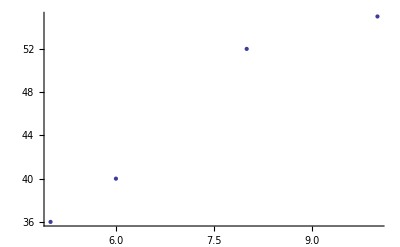

```mathematica
ListPlot[{{5,36},{6,40},{8,52},{10,55}},AxesOrigin->{4.8,30}]
```

```mathematica
f=FindFit[{{5,36},{6,40},{8,52},{10,55}},a+b/n,{a,b},n]
```

{a→75.9617,b→-204.248}

```mathematica
Table[a+b/n/.f,{n,{5,6,8,10}}]
```

{35.1121,41.9204,50.4307,55.5369}

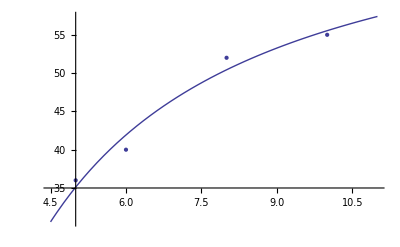

```mathematica
Show[{Plot[a+b/n/.f,{n,4.5,11}],ListPlot[{{5,36},{6,40},{8,52},{10,55}}]}]
```

```mathematica
f=FindFit[{{5,36},{6,40},{8,52},{10,55}},a+b n,{a,b},n]
```

{a→16.6271,b→4.01695}

```mathematica
Table[a+b n/.f,{n,{5,6,8,10}}]
```

{36.7119,40.7288,48.7627,56.7966}

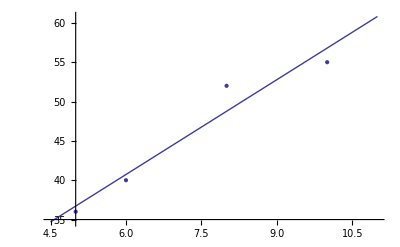

```mathematica
Show[{Plot[a+b n/.f,{n,4.5,11}],ListPlot[{{5,36},{6,40},{8,52},{10,55}}]}]
```

### PSOpti4 score plotting

```mathematica
7984+7983+8128+8122+8145+8319
```

48681

```mathematica
828.5+585.5+429-83.5+461+93
```

2313.5

```mathematica
2313.5/48681
```

0.0475237

```mathematica
5.2*1000/√48681
```

23.568

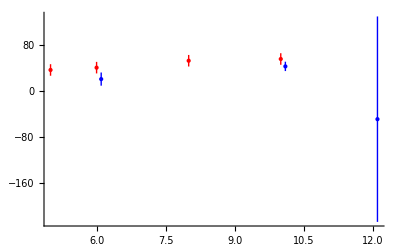

```mathematica
Needs["ErrorBarPlots`"]
Bit[won_,ngames_,bin_]:={{bin,1000 won/ngames},ErrorBar[2 6000/√ngames]}
With[{mine=0.1},ErrorListPlot[{
{{{6+mine,20.2},ErrorBar[11.4]},{{10+mine,42.2},ErrorBar[8.087]},Bit[-72.5-151.5,3487+1065,12+mine]},
{{{5,36},ErrorBar[10]},{{6,40},ErrorBar[10]},{{8,52},ErrorBar[10]},{{10,55},ErrorBar[10]}}},
AxesOrigin->{4.5,0},PlotRange->All,PlotStyle->{Blue,Red}]]
```

```mathematica
1760+1411+859-1290+1789.5+1073.5
```

5603.

### Tourney Risk of Ruin

```mathematica
With[{ buyin=1,rake=0.1},
ProbBroke[bankroll_,goal_,p_,nmax_,n_:1]:=If[n>nmax,
With[{ap=p-rake/(2buyin),ngw=(goal-bankroll)/buyin,ngl=(bankroll-buyin)/buyin},{ap^ngw/(ap^ngw+(1-ap)^ngl),0,(1-ap)^ngl/(ap^ngw+(1-ap)^ngl)}],
If[bankroll<buyin,{0,0,1},
If[bankroll>goal,{1,0,0},
p ProbBroke[bankroll+buyin-rake,goal,p,nmax,n+1]+(1-p)ProbBroke[bankroll-buyin-rake,goal,p,nmax,n+1]]]]]
```

```mathematica
100ProbBroke[5.25,25,.60,20]//Column
```

19.1484
0
80.8516

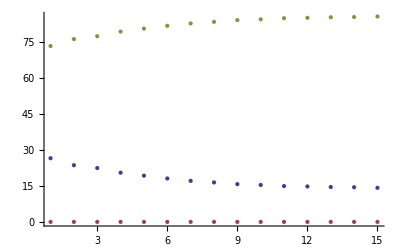

```mathematica
ListPlot[Table[100ProbBroke[5.25,8,.40,i],{i,1,15}]//Transpose]
```